Kaushik Chakram 
                                                                                                                                     phys 425 &01
                                                                                                                     Professor Julia Kamenetzky
                                                                                                                     January 25,2018

Problem 1.3 a) Checking the integral value that I got.

```mathematica
Integrate[A*ⅇ^(-λ(x-a)^2),{x,-Infinity,Infinity}]
```

ConditionalExpression[(A √π)/(√λ),Re[λ]≥0]

1.3 b) Checking the integral value that I got. Even if we did the below integrals via U-sub. this show that we get the same result (see just below).

```mathematica
Integrate[√(λ/π)*(u+a)*ⅇ^(-λ(u)^2),{u,-Infinity,Infinity}]
```

ConditionalExpression[a,Re[λ]>0]

```mathematica
Integrate[√(λ/π)*(x)*ⅇ^(-λ(x-a)^2),{x,-Infinity,Infinity}]
```

ConditionalExpression[a,Re[λ]≥0]

```mathematica
Integrate[√(λ/π)*(x)^2*ⅇ^(-λ(x-a)^2),{x,-Infinity,Infinity}]
```

ConditionalExpression[(1+2 a^2 λ)/(2 λ),Re[λ]≥0]

1.3) c) Defining Piecewise function here. Also plotting the Gaussian function with a = 2 and λ= π.

```mathematica
Piecewise[{{λ/π,x==a},{√(λ/π)*ⅇ^(-λ(x-a)^2),x≠ a}}]
```

Piecewise[{{λ/π, x==a}, {(ⅇ^(-(-a+x)^2 λ) √λ)/(√π), x≠a}, {0, True}}]

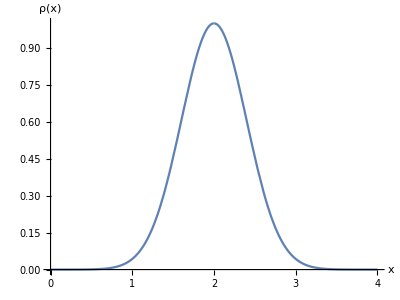

```mathematica
Plot[Piecewise[{{π/π,g==2},{√(π/π)*ⅇ^(-π*(g-2)^2),g≠2}}],{g,0,4},AspectRatio->3/4,AxesLabel->{x,"ρ(x)"},AxesStyle->Directive[Black, 14]]
```

Problem 3) 1.5)a) Checking the integral value that I got.

```mathematica
Integrate[ⅇ^(-2*λ*Abs[x]),{x,-Infinity,Infinity}]
```

Piecewise[{{1/λ, Re[λ]>0}, {Integrate[ⅇ^(-2 λ Abs[x]),{x,-∞,∞},Assumptions→Re[λ]≤0], True}}]

Problem 3) 1.5) b) Checking the integral value that I got.

```mathematica
Integrate[x*ⅇ^(-2*λ*Abs[x]),{x,-Infinity,Infinity}]
```

Piecewise[{{0, Re[λ]>0}, {Integrate[ⅇ^(-2 λ Abs[x]) x,{x,-∞,∞},Assumptions→Re[λ]≤0], True}}]

We let λ = 1 for this part to show the graph below our σ becomes σ = 1/(√2).

```mathematica
μ:=0
σ:= 1/(√2)
```

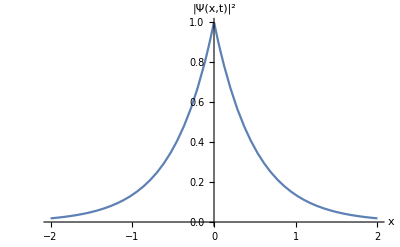

```mathematica
Plot[Piecewise[{{1,h==0},{ⅇ^(-2*(h)),h>0},{ⅇ^(2*(h)),h<0}}],{h,-2,2},AxesLabel->{x,"|Ψ(x,t)|^2"},AxesStyle->Directive[Black, 15],GridLines->{{μ-σ,μ+σ},{}}]
```

Problem 4)1.11)a) This is a plot of the probability density ρ(θ). Notice we get a uniform distribution.

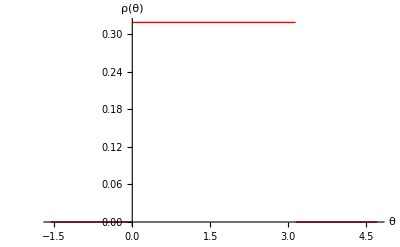

```mathematica
Plot[Piecewise[{{1/π,0≤ d≤π}}],{d,-π/2,(3π)/2},AxesLabel->{θ,"ρ(θ)"},AxesStyle->Directive[Black,15],PlotStyle->{Thick,Red}]
```